## Import application packages

```mathematica
<<ProbabilisticBricks`
```

## Increasing horizontal loads - plastic zone expansion

### Problem initialization

Set the geometry and other parameters using setProblemProperties[nelx, nely, b, h, P, μ], where nelx is the number of bricks per course, nely the number of courses, b and h are the dimensions of the brick, P is the weight of a brick and μ the static friction coefficient

```mathematica
setProblemProperties[50,70,3,1,0.1,0.7];
```

Generate random contacts

```mathematica
generateContacts[];
```

### Compute frames

```mathematica
tmax=12.9;
frames={};
For[t=0,t≤tmax,t+=0.3,
p=Table[{0,0,0,0,0,0},{nelx}];
p[[5;;8]]={0,0,20,t,0,0};
p=Flatten[p];
setBoundaryConditions[p];
solveProblem[];
AppendTo[frames,displayWallWithFilter["stress_state"]];
];
```

### Generate & export animation

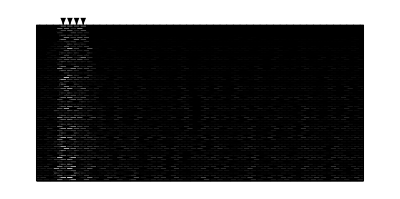
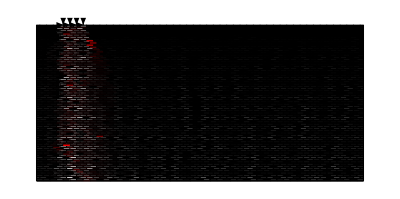
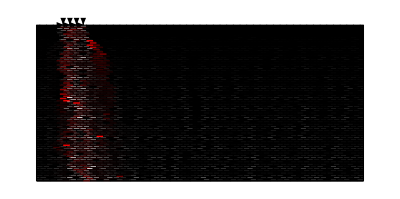
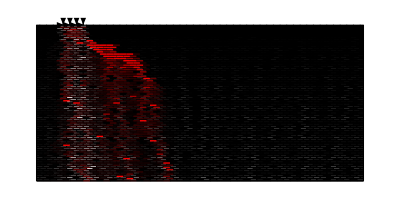
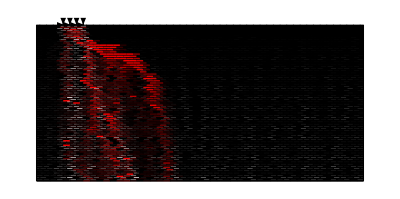
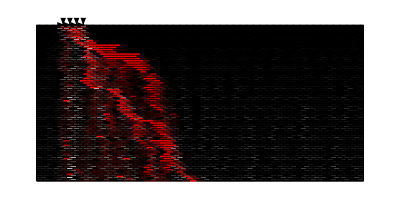
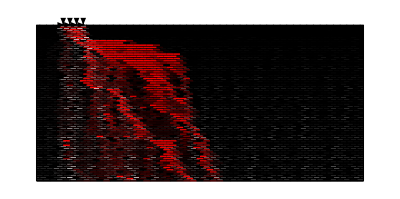
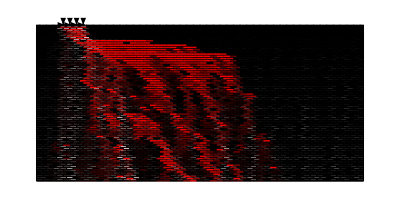

```mathematica
frames[[;;;;4]]
```

```mathematica
ListAnimate[frames]
```

$Aborted[]

#### Export frames as a video

```mathematica
Export["increasing_h_loads.avi",frames,"FrameRate"->3,ImageSize->{1000,Automatic}]
```

increasing_h_loads.avi

#### Export every frame as a pdf

```mathematica
Do[
Export["frame_"<>ToString[i]<>".pdf",frames[[i]],ImageSize->1000],
{i,Length[frames]}
];
```